# 有限长度纵向 PEEC

## 缪雨轩 / Miao Yuxuan · 淮南师范学院 / Huainan Normal University

## 模型、输入与适用范围

Z=R+jωL; Zi=V1; 1ᵀi=It

SI; exp(+j omega t); RMS; sigma=58 MS/m; mu_r=1; 20 C

修改长度或横向离散，核对复端口约束与功率。基函数沿纵向。

## 推导与结果解释

将截面离散为纵向电流基函数。磁准静态积分方程经 Galerkin 投影得到 Z=R+jωL；R 由电导率与基函数重叠构造，L 含有限长度互项与自项。

联立 Zi=V1、1ᵀi=It 求未知端电压与复电流。有功输入须与电阻二次型损耗 iᴴRi 一致。

横向离散、轴向长度和积分阶数分别研究。纵向基函数未保留一般横向电流及完整端区电荷，适用范围应据此解释。

```mathematica
projectRoot=NestWhile[DirectoryName,NotebookDirectory[],!FileExistsQ[FileNameJoin[{#1,"pyproject.toml"}]]&&DirectoryName[#1]=!=#1&];Get[FileNameJoin[{projectRoot,"shared","wolfram","ResearchNotebook.wl"}]];
```

## 可编辑参数

```mathematica
parameters=<|"cross_divisions"->6,"length_m"->0.04,"frequency_Hz"->200000.,"quadrature_order"->4|>;parameters
```

<|cross_divisions -> 6, length_m -> 0.04, frequency_Hz -> 200000., 
 
>   quadrature_order -> 4|>

## 独立进程执行与结果

```mathematica
research=LitzNotebook`RunResearch[projectRoot,"peec",parameters];LitzNotebook`ResearchSummary[research]
```

<|run_id -> notebook_peec_20261014005900_c670b5e6, 
 
>   source_model -> finite_length_longitudinal_volume_filament_PEEC, 
 
>   execution_status -> completed, 
 
>   physical_acceptance_status -> passed_test_scope_only|>

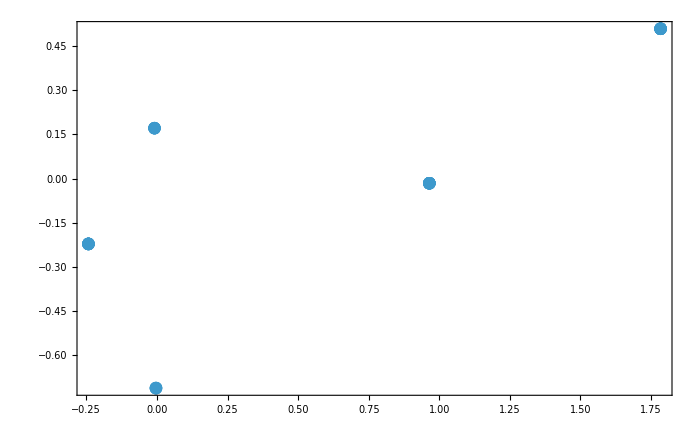

```mathematica
LitzNotebook`DisplayResearch[research]
```

## 验收与接续

核对结果中的 checks、execution_status 和 physical_acceptance_status。完整收敛与结构研究按路线 README 继续。

Sources: P03, RUEHLI1974; references/library.bib and references/sources.json

## 历史证据

data/evidence/v1.0.0-rc.1/; litz-research data fetch peec